Here is the full reproduction of the formula:
Π(x) = li(x)-Σ li(x^ρ)-log2 +(∫_x)^∞dt/(t(t^2-1)log t)
According to the the Wiki page li(x^ρ) should be replaced with Ei(ρ log x) and to account for the branch-cut ambiguity, ρ* is used instead of ρ. You can see, that 100 pairs of zeros approximate the true Riemann prime counting function quite accurately.

```mathematica
Π[x_,n_]:=LogIntegral[x]-Log[2]+NIntegrate[1/(t (t^2-1) Log[t]),{t,x,∞}]-2Sum[Re[ExpIntegralEi[ZetaZero[k]*Log[x]]],{k,1,n}]
Π2[x_,n_]:=Sum[Sum[If[Prime[k]^l≤x,1/l,0],{l,1,Floor[Log[2,x]]}],{k,1,n}]
```

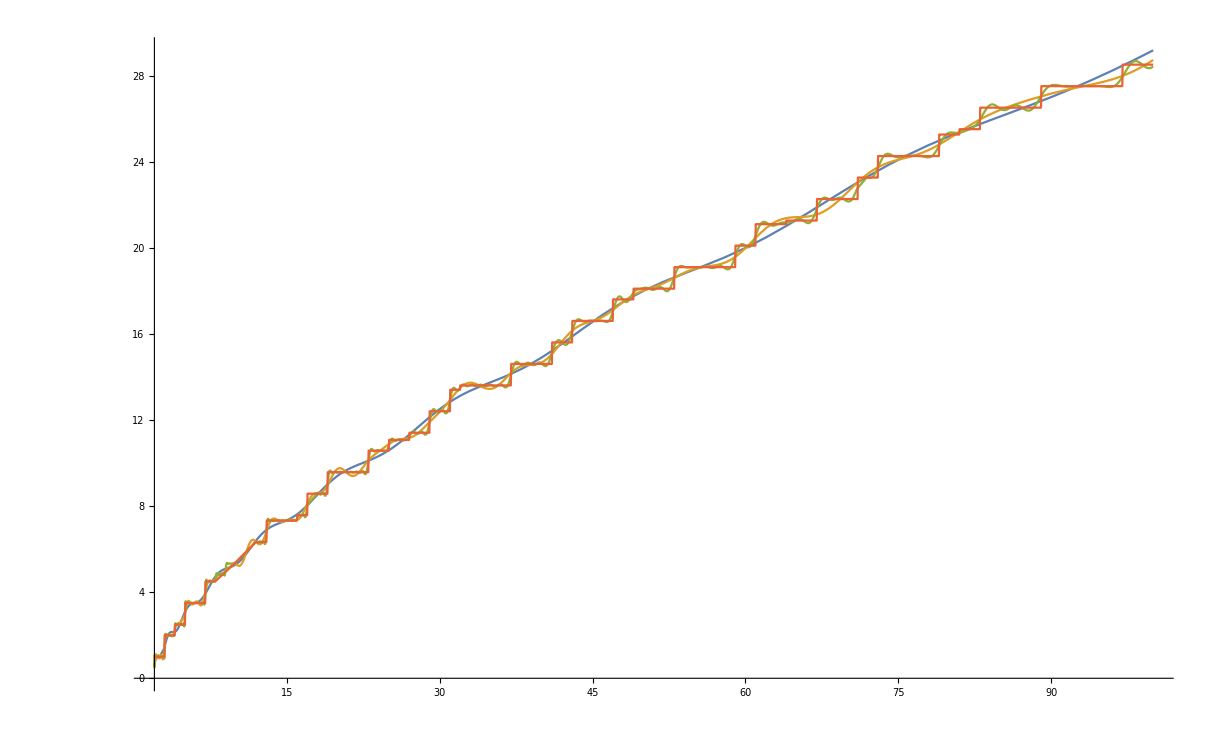

```mathematica
Plot[{Π[x,1],Π[x,10],Π[x,100],Π2[x,100]},{x,2,100},PlotPoints->100]
```